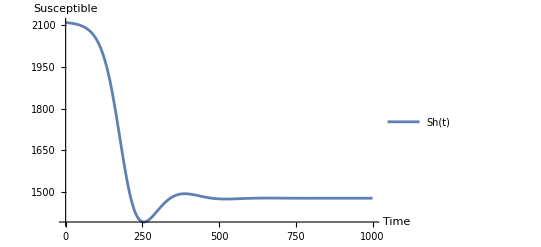

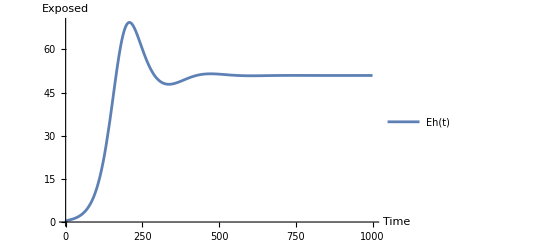

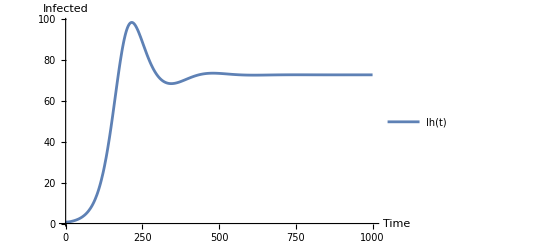

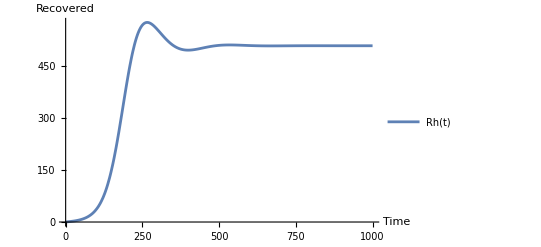

```mathematica
beta =0.2;sigma =0.2;gamma = 0.14;omega = 0.02;

Nh = Sh+Eh+Ih+Rh;

dShdt[Sh_,Eh_,Ih_,Rh_] = (-beta*((Sh*Ih)/Nh))+(omega*Rh);
dEhdt[Sh_,Eh_,Ih_,Rh_] = (beta*((Sh*Ih)/Nh))-sigma*Eh;
dIhdt[Sh_,Eh_,Ih_,Rh_] = (sigma*Eh)-(gamma*Ih);
dRhdt[Sh_,Eh_,Ih_,Rh_] = (gamma*Ih)-(omega*Rh);



Sh0=2110;Eh0=0;Ih0=1; Rh0=0;
finalTime = 1000;


sol=NDSolve[{
Sh'[t]==dShdt[Sh[t],Eh[t],Ih[t],Rh[t]],
Eh'[t]==dEhdt[Sh[t],Eh[t],Ih[t],Rh[t]],
Ih'[t]==dIhdt[Sh[t],Eh[t],Ih[t],Rh[t]],
Rh'[t]==dRhdt[Sh[t],Eh[t],Ih[t],Rh[t]],
Sh[0]==Sh0,Eh[0]==Eh0,Ih[0]==Ih0,Rh[0]== Rh0},{Sh,Eh,Ih,Rh},{t,0,finalTime}];

Plot[Evaluate[{Sh[t]}/.sol],{t,0,finalTime},AxesLabel->{"Time","Susceptible "},PlotRange->All,PlotLegends->{"Sh(t)"}]
Plot[Evaluate[{Eh[t]}/.sol],{t,0,finalTime},AxesLabel->{"Time","Exposed "},PlotRange->All,PlotLegends->{"Eh(t)"}]
Plot[Evaluate[{Ih[t]}/.sol],{t,0,finalTime},AxesLabel->{"Time","Infected "},PlotRange->All,PlotLegends->{"Ih(t)"}]            
Plot[Evaluate[{Rh[t]}/.sol],{t,0,finalTime},AxesLabel->{"Time","Recovered "},PlotRange->All,PlotLegends->{"Rh(t)"}]
```